# 360 HW 21

## Problem 1

-Graphics-

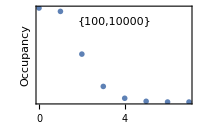

```mathematica
size=100;
grid=ConstantArray[1,{size,size}];
gridmove[]:=Module[{xA,yA,xB,yB},
xA=RandomInteger[{1,size}];
yA=RandomInteger[{1,size}];
xB=RandomInteger[{1,size}];
yB=RandomInteger[{1,size}];
If[grid[[xA,yA]]>0,grid[[xB,yB]]=grid[[xB,yB]]+1,grid[[xB,yB]]];
If[grid[[xA,yA]]>0,grid[[xA,yA]]=grid[[xA,yA]]-1 ,grid[[xA,yA]]];
]
movenum=10^4;
Do[gridmove[],movenum]
ArrayPlot[grid]
boltzman=Sort[Tally[Flatten[grid]]];
ListPlot[boltzman,PlotRange->All,Frame->True,PlotStyle->PointSize[0.02],BaseStyle->{FontSize->12},FrameLabel->{"Energy Level","Occupancy"}, ImageSize->200,FrameTicks->{Automatic,None},Epilog->Inset[{Text[size],Text[movenum]},Scaled[{0.5,0.85}]]]
```

## Problem 2

### Part A

```mathematica
sizearray=100;
gridarray=ConstantArray[1,{sizearray,sizearray}];
gridmovearrayplot[]:=Module[{xA,yA,xB,yB},
xA=RandomInteger[{1,sizearray}];
yA=RandomInteger[{1,sizearray}];
xB=RandomInteger[{1,sizearray}];
yB=RandomInteger[{1,sizearray}];
If[gridarray[[xA,yA]]>0,gridarray[[xB,yB]]=gridarray[[xB,yB]]+1,gridarray[[xB,yB]]];
If[gridarray[[xA,yA]]>0,gridarray[[xA,yA]]=gridarray[[xA,yA]]-1 ,gridarray[[xA,yA]]];
]
dogridmovearrayplot[g_]:=Module[{movenumarray},
movenumarray=10^g;
Do[gridmovearrayplot[],movenumarray];
boltzman=Sort[Tally[Flatten[gridarray]]];
ArrayPlot[gridarray]
]
sizelist=100;
gridlist=ConstantArray[1,{sizelist,sizelist}];
gridmovelistplot[]:=Module[{xA,yA,xB,yB},
xA=RandomInteger[{1,sizelist}];
yA=RandomInteger[{1,sizelist}];
xB=RandomInteger[{1,sizelist}];
yB=RandomInteger[{1,sizelist}];
If[gridlist[[xA,yA]]>0,gridlist[[xB,yB]]=gridlist[[xB,yB]]+1,gridlist[[xB,yB]]];
If[gridlist[[xA,yA]]>0,gridlist[[xA,yA]]=gridlist[[xA,yA]]-1 ,gridlist[[xA,yA]]];
]
dogridmovelistplot[g_]:=Module[{movenum},
movenum=10^g;
Do[gridmovelistplot[],movenum];
boltzman=Sort[Tally[Flatten[gridlist]]];
ListPlot[boltzman,PlotRange->All,Frame->True,PlotStyle->PointSize[0.02],BaseStyle->{FontSize->12},FrameLabel->{"Energy Level","Occupancy"}, ImageSize->200,FrameTicks->{Automatic,None},Epilog->Inset[{Text[size],Text[movenum]},Scaled[{0.5,0.85}]]]
]
g={0,0,0,0,0,0};
e={0,0,0,0,0,0};
i=2;While[i<7,g[[i]]=dogridmovearrayplot[i];i++]
i=2;While[i<7,e[[i]]=dogridmovelistplot[i];i++]
GraphicsGrid[{{g[[2]],e[[2]]},{g[[4]],e[[4]]},{g[[5]],e[[5]]},{g[[6]],e[[6]]}},ImageSize->500]
```

-Graphics-

### Part B

The probability distribution gets closer and closer to looking like an exponential graph as movenum increases. I find it interesting that there is such a great number of values of 1. The appearance of the plots stop changing at about 10^5 movenum.

### Part C

This occurs because the microstates of the same Boltzman macrostates have the same internal energy. This is what it means to be in contact with a thermal reservoir in statistical mechanics. However, the microstates are not all equally probable, but they are referred to as a canonical ensemble.

## Problem 3

### Part A

```mathematica
dogridmovelist[g_]:=Module[{movenum},
movenum=10^g;
Do[gridmovelistplot[],movenum];
boltzman=Sort[Tally[Flatten[gridlist]]]
]
```

```mathematica
fit=NonlinearModelFit[dogridmovelist[5],a*Exp[-b*x],{a,b},x]
```

FittedModel[4992.08 ⅇ^(-0.69004 x)]

```mathematica
A=4992.08;
B=-0.69004;
```

### Part B

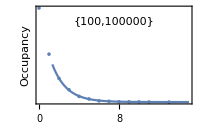

```mathematica
Show[ListPlot[dogridmovelist[5]],Plot[4992.08*Exp[-0.69004*x],{x,0,15}],PlotRange->All,Frame->True,PlotStyle->PointSize[0.02],BaseStyle->{FontSize->12},FrameLabel->{"Energy Level","Occupancy"}, ImageSize->200,FrameTicks->{Automatic,None},Epilog->Inset[{Text[sizelist],Text[100000]},Scaled[{0.5,0.85}]]]
```

### Part C

```mathematica
lambda=0.69004;
epsilon=20*10^-3*1.602*10^-19;
k=1.38*10^-23;
T=((lambda*k)/epsilon)^-1
```

336.464

### Part D

```mathematica
lambda=epsilon/(k*T);
```

When Q = N,epsilon/(k*T)=ln((2u+epsilon)/(2u-epsilon))=ln((2u/epsilon+1)/(2u/epsilon-1))=ln(2)

```mathematica
N[Log[2]]
```

0.693147

Therefore, ln(2) is approximately equal to the value I got for lambda : 0.69004